MS

prevalence

```mathematica
(* http://www.phac-aspc.gc.ca/publicat/cd-mc/mc-ec/section-3-eng.php
```

```mathematica
s=Import["Projects/Autoimmune/autoimmunems.xlsx"];
```

```mathematica
s=s[[1]];
```

```mathematica
msmale=Drop[Drop[s,0,{4}],0,{2}];
```

```mathematica
msfemale=Drop[Drop[s,0,{3}],0,{2}];
```

```mathematica
msmalelog=msmale;
```

```mathematica
msmalelog[[All,2]]=Log[msmalelog[[All,2]]];
```

```mathematica
msmalem=NonlinearModelFit[msmalelog,A -k Exp[-d t]-0.045 t,{A,{k,20},{c,0.15},{d,0.01}},t]
```

FittedModel[8.41274-12.5744 ⅇ^(-«21» t)-0.045 t]

```mathematica
msmalem["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 8.41274 | 0.23541 | 35.7365 | 9.90612×10^-13
k | 12.5744 | 1.49956 | 8.38539 | 4.16465×10^-6
c | 0.15 | 0. | ∞ | 0.
d | 0.0477138 | 0.0068015 | 7.01518 | 0.0000222511

```mathematica
msfemalelog=msfemale;
```

```mathematica
msfemalelog[[All,2]]=Log[msfemalelog[[All,2]]];
```

```mathematica
msfemalem=NonlinearModelFit[msfemalelog,A -k Exp[-d t]-0.045 t,{A,{k,20},{c,0.15},{d,0.01}},t]
```

FittedModel[9.06228-15.5112 ⅇ^(-«19» t)-0.045 t]

```mathematica
msfemalem=NonlinearModelFit[msfemale,A Exp[-k Exp[-d t]]Exp[-0.045 t]-b (1-Exp[-m Exp[-d t]])Exp[-0.045t],{{A,10000},{k,40},{b,100},{m,40},{d,0.05}},t]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[8994.64 ⅇ^(-34.1373 «1»-«1»)-102288. «1» (1-«1»)]

```mathematica
msmalem=NonlinearModelFit[msmale,A Exp[-k Exp[-d t]]Exp[-0.045 t]-b (1-Exp[-m Exp[-d t]])Exp[-0.045t],{{A,10000},{k,40},{b,100},{m,40},{d,0.05}},t]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[4489.46 ⅇ^(-27.2014 «1»-«1»)-53922.2 ⅇ^(«1») (1-ⅇ^(«1»))]

```mathematica
msfemalem=NonlinearModelFit[msfemale,A Exp[-k Exp[-d t]]Exp[-0.045 t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[9088.81 ⅇ^(-30.9609 «1»-«1»)]

```mathematica
msfemalem
```

FittedModel[8867.5 ⅇ^(-40.1085 «1»«1»«1»)«1»93.571 «1»«1»(1-«1»)]

```mathematica
%57["Function"]
```

8867.5 ⅇ^(-40.1085 ⅇ^(-0.0837443 #1)-0.045 #1)+93.571 ⅇ^(-0.045 #1) (1-ⅇ^(-40.1086 ⅇ^(-0.0837443 #1)))&

```mathematica
msfemalem["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 9088.81 | 1048.26 | 8.67038 | 1.63439×10^-6
k | 30.9609 | 12.6258 | 2.45219 | 0.0304709
d | 0.0777322 | 0.0121349 | 6.40567 | 0.0000337405

```mathematica
msmale
```

{{17.,10.},{22.,20.},{27.,30.},{32.,60.},{37.,90.},{42.,110.},{47.,150.},{52.,160.},{57.,210.},{62.,200.},{67.,180.},{72.,150.},{77.,100.},{82.,80.},{92.,30.}}

```mathematica
msmale[[1,2]]
```

10.

```mathematica
msmalenegsel=Table[{msmale[[i,1]],msmale[[i,2]]*Exp[0.05*msmale[[i,1]]]},{i,Length[msmale]}];
```

```mathematica
msfemalenegsel=Table[{msfemale[[i,1]],msfemale[[i,2]]*Exp[0.05*msfemale[[i,1]]]},{i,Length[msfemale]}];
```

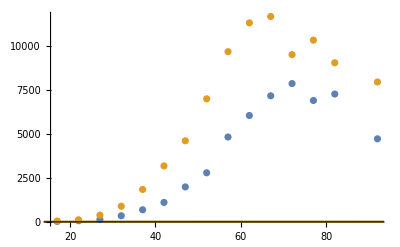

```mathematica
Show[ListPlot[{msmalenegsel,msfemalenegsel}],Plot[{msmalem[t],msfemalem[t]},{t,0,95}]]
```

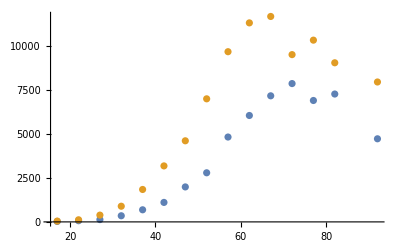

```mathematica
Show[ListPlot[{msmalenegsel,msfemalenegsel}],Plot[{},{t,0,95}]]
```

```mathematica
(* Adding Tregs doesn't do much *)
```

```mathematica
(* Ratio of T to Treg *)
```

```mathematica
msfemalem=NonlinearModelFit[msfemalelog,A -k Exp[-d t]-Log[ (1-Exp[-m Exp[-d t]])],{{A,10},{k,10},{m,1},{d,0.05}},t]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[6.23405-3.4705 «1»-Log[1-ⅇ^(-28.6951«1»«1»)]]

```mathematica
msmalem=NonlinearModelFit[msmalelog,A -k Exp[-d t]-Log[ (1-Exp[-m Exp[-d t]])],{{A,100},{k,10},{m,10},{d,0.05}},t]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[-1474.97+1478.32 ⅇ^(«1»)-Log[1-ⅇ^(-72.6207 «1»)]]

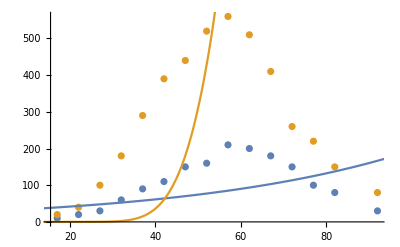

```mathematica
Show[ListPlot[{msmale,msfemale}],Plot[{Exp[msmalem[t]],Exp[A -k Exp[-d t]-Log[ (1-Exp[-m Exp[-d t]])]//.{A->9,k->40,m->47,d->0.05}]},{t,0,95}]]
```

```mathematica
(* Doesn't work *)
```

Lupus http://ard.bmj.com/content/suppl/2014/09/29/annrheumdis-2014-206334.DC1/annrheumdis-2014-206334supp_tables.pdf

```mathematica
s=Import["Projects/Autoimmune/autoimmunelupus.xlsx"];
```

```mathematica
s=s[[1]];
```

```mathematica
lupumalefemale=Drop[Drop[s,14,0],0,{2,8}];
```

```mathematica
msfemalelog=lupumalefemale;
```

```mathematica
msfemalelog[[All,2]]=Log[msfemalelog[[All,2]]];
```

```mathematica
msfemalem=NonlinearModelFit[msfemalelog,A -k Exp[-d t]-0.045 t,{A,{k,10},{c,0.05},{d,0.05}},t]
```

FittedModel[5.227-8.10766 ⅇ^(-«20» t)-0.045 t]

```mathematica
msfemalem["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 5.227 | 0.172306 | 30.3355 | 8.51499×10^-8
k | 8.10766 | 0.347315 | 23.3438 | 4.05307×10^-7
c | 0.05 | 0. | ∞ | 0.
d | 0.0448104 | 0.00449569 | 9.96741 | 0.0000590078

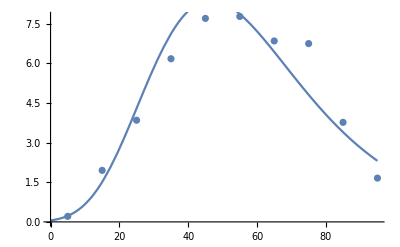

```mathematica
Show[ListPlot[{lupumalefemale}],Plot[{Exp[msfemalem[t]]},{t,0,95}]]
```

```mathematica
RA http://www.ncbi.nlm.nih.gov/pmc/articles/PMC2929692/
```

```mathematica
s=Import["Projects/Autoimmune/autoimmuneRA.xlsx"];
```

```mathematica
s=s[[1]];
```

```mathematica
msmale=Drop[Drop[s,5,0],0,{2}][[All,{1,2}]];
```

```mathematica
msfemale=Drop[Drop[s,5,0],0,{2}][[All,{1,4}]];
```

```mathematica
msmalelog=msmale;
```

```mathematica
msmalelog[[All,2]]=Log[msmalelog[[All,2]]];
```

```mathematica
msmalem=NonlinearModelFit[msmalelog,A -k Exp[-d t]-0.045 t,{A,{k,20},{c,0.15},{d,0.01}},t]
```

FittedModel[8.23085-14.3717 ⅇ^(-«20» t)-0.045 t]

```mathematica
msmalem["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 8.23085 | 0.613684 | 13.4122 | 0.000896081
k | 14.3717 | 2.61618 | 5.49337 | 0.0118694
c | 0.15 | 0. | ∞ | 0.
d | 0.0357653 | 0.00940809 | 3.80155 | 0.0319709

```mathematica
msfemalelog=msfemale;
```

```mathematica
msfemalelog[[All,2]]=Log[msfemalelog[[All,2]]];
```

```mathematica
msfemalem=NonlinearModelFit[msfemalelog,A -k Exp[-0.04 t]-0.045 t,{A,{k,10},{c,0.05},{d,0.05}},t]
```

FittedModel[8.42419-13.0027 ⅇ^(-0.04 t)-0.045 t]

```mathematica
msfemalem["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 8.42419 | 0.152713 | 55.1634 | 0.0000131221
k | 13.0027 | 0.884329 | 14.7034 | 0.000682388
c | 0. | 0. | ComplexInfinity | 0.
d | 0. | 0. | ComplexInfinity | 0.

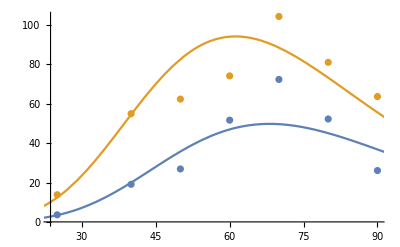

```mathematica
Show[ListPlot[{msmale,msfemale}],Plot[{Exp[msmalem[t]],Exp[msfemalem[t]]},{t,0,95}]]
```

Long covid

prevalence

```mathematica
s=Import["Projects/Autoimmune/AutoimmuneLongCovid.xlsx"];
```

```mathematica
s=s[[1]];
```

```mathematica
s
```

{{LONG COVID,,https://www.ons.gov.uk/peoplepopulationandcommunity/healthandsocialcare/conditionsanddiseases/datasets/alldatarelatingtoprevalenceofongoingsymptomsfollowingcoronaviruscovid19infectionintheuk,,},{Table 5. Estimated percentage of people living in private households with self-reported long COVID who first had (or suspected they had) COVID-19 at least 12 weeks previously, UK: four week period ending 6 December 2021,,,,},{,,,,Percent},{Domain,Group,Estimate,Lower 95% confidence limit,Upper 95% confidence limit},{All people,All people,1.38,1.33,1.43},{Age group,2 to 11,0.21,0.14,0.29},{,12 to 16,0.82,0.68,0.96},{,17 to 24,1.31,1.11,1.52},{,25 to 34,1.4,1.24,1.56},{,35 to 49,1.98,1.86,2.11},{,50 to 69,1.95,1.86,2.04},{,70+,0.79,0.72,0.86},{Sex,Male,1.16,1.1,1.23},{,Female,1.59,1.52,1.66},{,,,,},{https://www.medrxiv.org/content/10.1101/2020.10.19.20214494v2.full-text,,,,}}

```mathematica
Drop[Drop[s,5,{}],-4,{1,2,3}][[All,2]]
```

{0.21,0.82,1.31,1.4,1.98,1.95,0.79}

```mathematica
lcdata=Table[Drop[Drop[s,5,{}],-4,{1,2,3}][[i,2]],{i,1,7}]
```

{0.21,0.82,1.31,1.4,1.98,1.95,0.79}

```mathematica
lcdataerr=Table[Around[Drop[Drop[s,5,{}],-4,{1,2,3}][[i,2]],{Drop[Drop[s,5,{}],-4,{1,2,3}][[i,2]]-Drop[Drop[s,5,{}],-4,{1,2,3}][[i,3]],Drop[Drop[s,5,{}],-4,{1,2,3}][[i,4]]-Drop[Drop[s,5,{}],-4,{1,2,3}][[i,2]]}],{i,1,7}]
```

{0.210.070.08,0.820.140.14,1.310.200.21,1.400.160.16,1.980.120.13,1.950.090.09,0.790.070.07}

```mathematica
ages={6,14,20,30,40,60,80}
```

{6,14,20,30,40,60,80}

```mathematica
lc=Table[{ages[[i]],lcdata[[i]]},{i,1,Length[ages]}]
```

{{6,0.21},{14,0.82},{20,1.31},{30,1.4},{40,1.98},{60,1.95},{80,0.79}}

```mathematica
lcerr=Table[{ages[[i]],lcdataerr[[i]]},{i,1,Length[ages]}]
```

{{6,0.210.070.08},{14,0.820.140.14},{20,1.310.200.21},{30,1.400.160.16},{40,1.980.120.13},{60,1.950.090.09},{80,0.790.070.07}}

```mathematica
lcm=NonlinearModelFit[lc,A Exp[-k Exp[-d t]]Exp[-0.045 t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[55.7896 ⅇ^(-5.91752 «1»-«1»)]

```mathematica
lcm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 55.7896 | 22.5364 | 2.47553 | 0.0685389
k | 5.91752 | 0.529686 | 11.1717 | 0.000365442
d | 0.0335996 | 0.00805445 | 4.17155 | 0.0140136

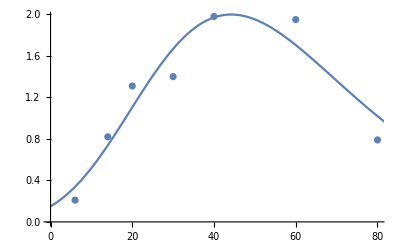

```mathematica
Show[ListPlot[{lc}],Plot[{lcm[t]},{t,0,95}]]
```

```mathematica
lcnegsel=Table[{lc[[i,1]],lc[[i,2]]*Exp[0.045*lc[[i,1]]]},{i,Length[lc]}];
```

```mathematica
lcnegselerr=Table[{lc[[i,1]],lcerr[[i,2]]*Exp[0.045*lc[[i,1]]]},{i,Length[lc]}];
```

```mathematica
lcnegselm=NonlinearModelFit[lcnegsel,A Exp[-k Exp[-0.045 t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[37.6046 ⅇ^(-6.37841 «1»)]

```mathematica
lcnegselm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 37.6046 | 3.62193 | 10.3825 | 0.000485909
k | 6.37841 | 1.12456 | 5.67189 | 0.00476654
d | 0.05 | 0. | ∞ | 0.

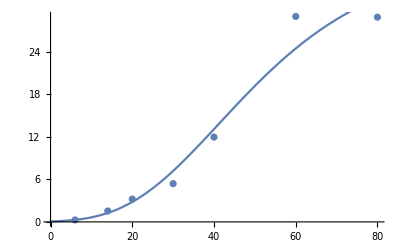

```mathematica
Show[ListPlot[{lcnegsel}],Plot[{lcnegselm[t]},{t,0,95}]]
```

MS

incidence

```mathematica
s=Import["Projects/Autoimmune/autoimmuneMSincprev.xlsx"];
```

```mathematica
s=s[[1]];
```

```mathematica
s
```

{{,pop,incidence,,prevalence,,,,},{Male,,,,,,,,},{ Under 10,3738.8,0.04,2.,0.3,12.,,,},{ 10–19,3838.,0.41,16.,2.4,92.,,,},{ 20–29,4381.7,3.85,169.,19.6,860.,,,},{ 30–39,4044.4,7.25,293.,88.8,3593.,,,},{ 40–49,4543.6,9.34,425.,166.5,7568.,,,},{ 50–59,3723.4,10.12,377.,248.6,9259.,,,},{ 60–69,3252.2,8.21,267.,287.,9336.,,,},{ 70–79,2054.2,7.2,148.,183.9,3779.,,,},{ 80–89,933.2,6.11,57.,72.7,679.,,,},{ 90 Plus,133.8,0.,0.,35.6,48.,,,},{ Total,30 643.3,5.72,1754.,114.9,35 225,,,},{Female,,,,,,,,},{ Under 10,3566.,0.09,3.,0.2,10.,,,},{ 10–19,3640.5,1.43,52.,3.,110.,,,},{ 20–29,4177.9,11.62,486.,58.4,2440.,,,},{ 30–39,4048.8,20.41,827.,274.,11 095,,,},{ 40–49,4654.7,24.4,1136.,470.2,21 887,,,},{ 50–59,3836.3,22.12,849.,638.7,24 502,,,},{ 60–69,3443.1,14.7,506.,597.,20 555,,,},{ 70–79,2415.3,10.1,244.,340.8,8232.,,,},{ 80–89,1494.1,8.06,121.,156.6,2341.,,,},{ 90 Plus,342.3,7.62,26.,79.1,271.,,,},{ Total,31 619.0,13.44,4250.,289.2,91 444,,,},{,,,,,,,,},{https://jnnp.bmj.com/content/85/1/76,,,,,,,,}}

```mathematica
lcdata=Drop[Drop[s,2,{4}],-16,{1,2,3}][[All,2]]
```

{0.04,0.41,3.85,7.25,9.34,10.12,8.21,7.2,6.11}

```mathematica
ages=Range[5,85,10]
```

{5,15,25,35,45,55,65,75,85}

```mathematica
ms=Table[{ages[[i]],lcdata[[i]]},{i,1,Length[ages]}]
```

{{5,0.04},{15,0.41},{25,3.85},{35,7.25},{45,9.34},{55,10.12},{65,8.21},{75,7.2},{85,6.11}}

```mathematica
msm=NonlinearModelFit[lc,A Exp[-k Exp[-d t]]Exp[-0.045 t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[342.919 ⅇ^(-9.06618 «1»-«1»)]

```mathematica
msm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 342.919 | 47.5087 | 7.21804 | 0.000358389
k | 9.06618 | 0.778996 | 11.6383 | 0.0000242397
d | 0.0389597 | 0.003889 | 10.0179 | 0.0000573316

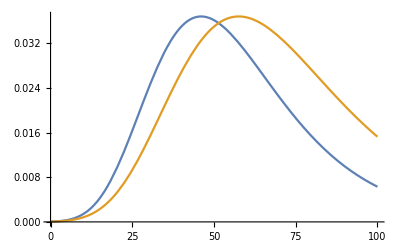

```mathematica
Plot[{Exp[-10Exp[-0.05 t]]Exp[-0.05 t],Exp[-10 Exp[-0.04 t]]Exp[-0.04 t]},{t,0,100}]
```

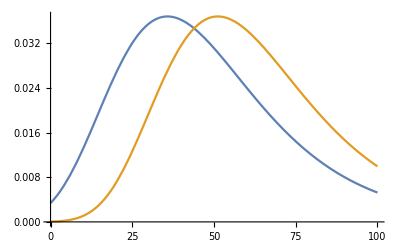

```mathematica
Plot[{0.5Exp[-5 Exp[-0.045 t]]Exp[-0.045 t],Exp[-10 Exp[-0.045 t]]Exp[-0.045 t]},{t,0,100}]
```

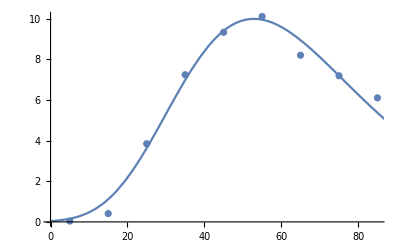

```mathematica
Show[ListPlot[{ms}],Plot[{msm[t]},{t,0,95}]]
```

```mathematica
lcnegsel=Table[{lc[[i,1]],lc[[i,2]]*Exp[0.045*lc[[i,1]]]},{i,Length[lc]}];
```

```mathematica
lcnegselm=NonlinearModelFit[lcnegsel,A Exp[-k Exp[-d t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[669.995 ⅇ^(-6.68777 «1»)]

```mathematica
lcnegselm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 669.995 | 190.586 | 3.51544 | 0.012588
k | 6.68777 | 0.697869 | 9.58314 | 0.000073799
d | 0.0237326 | 0.00465049 | 5.10326 | 0.0022143

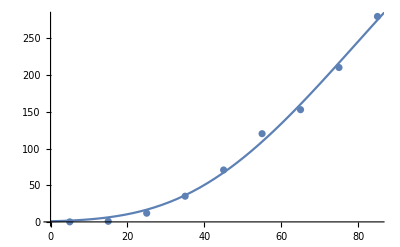

```mathematica
Show[ListPlot[{lcnegsel}],Plot[{lcnegselm[t]},{t,0,95}]]
```

```mathematica
s=Import["Projects/Autoimmune/autoimmuneMSincprev2.xlsx"];
```

```mathematica
s=s[[1]];
```

```mathematica
s
```

{{,pop,incidence,,inc2,,,},{Male,,,,,,,},{Under 10,841.,0.,1.,0.11,,,},{10–19,1146.2,0.52,7.,0.61,,,},{20–29,974.8,4.1,42.,4.3,,,},{30–39,1294.1,7.72,107.,8.26,,,},{40–49,1429.6,9.02,143.,10.,,,},{50–59,1301.4,7.45,123.,9.45,,,},{60–69,1013.5,5.22,75.,7.39,,,},{70–79,675.6,2.36,50.,7.4,,,},{80–89,296.2,1.35,14.,4.72,,,},{90 Plus,40.1,0.,4.,9.98,,,},{Total,9012.6,4.93,566.,6.28,,,},{Female,,,,,,,},{Under 10,804.1,0.,0.,0.,,,},{10–19,1035.,0.67,10.,0.96,,,},{20–29,870.3,12.75,121.,13.9,,,},{30–39,1250.,22.55,300.,23.99,,,},{40–49,1387.4,24.,358.,25.8,,,},{50–59,1277.1,17.46,270.,21.14,,,},{60–69,1035.5,10.04,142.,13.71,,,},{70–79,810.7,3.08,78.,9.62,,,},{80–89,499.2,1.4,35.,7.01,,,},{90 Plus,117.9,0.84,6.,5.08,,,},{ Total,31 619.0,4250.,289.2,91 444,,,},{,,,,,,,},{https://jnnp.bmj.com/content/85/1/76,,,,,,,}}

```mathematica
lcdata=Drop[Drop[s,2,{4}],-16,{1,2,3}][[All,3]]
```

{0.11,0.61,4.3,8.26,10.,9.45,7.39,7.4,4.72}

```mathematica
mspop=Drop[Drop[s,2,{4}],-16,{1,2,3}][[All,1]]*1000
```

{841000.,1.1462×10^6,974800.,1.2941×10^6,1.4296×10^6,1.3014×10^6,1.0135×10^6,675600.,296200.}

```mathematica
mscases=Drop[Drop[s,2,{}],-16,{1,2,3}][[All,3]]
```

{1.,7.,42.,107.,143.,123.,75.,50.,14.}

```mathematica
msprop=mscases/mspop
```

{1.18906×10^-6,6.10714×10^-6,0.0000430858,0.0000826829,0.000100028,0.0000945136,0.000074001,0.0000740083,0.0000472654}

```mathematica
ages=Range[5,85,10]
```

{5,15,25,35,45,55,65,75,85}

```mathematica
ms=Table[{ages[[i]],lcdata[[i]]},{i,1,Length[ages]}]
```

{{5,0.11},{15,0.61},{25,4.3},{35,8.26},{45,10.},{55,9.45},{65,7.39},{75,7.4},{85,4.72}}

```mathematica
mserr=Table[{ages[[i]],Around[lcdata[[i]],100000*1.96*√(msprop[[i]](1-msprop[[i]])/mspop[[i]])]},{i,1,Length[ages]}]
```

{{5,0.110.23},{15,0.60.5},{25,4.31.3},{35,8.31.6},{45,10.01.6},{55,9.41.7},{65,7.41.7},{75,7.42.1},{85,4.72.5}}

```mathematica
msm=NonlinearModelFit[ms,A Exp[-k Exp[-d t]]Exp[-0.045 t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[254.386 ⅇ^(-9.07525 «1»-«1»)]

```mathematica
msm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 254.386 | 37.0516 | 6.86571 | 0.000470321
k | 9.07525 | 1.09831 | 8.26294 | 0.00016997
d | 0.0446307 | 0.00541981 | 8.23472 | 0.000173241

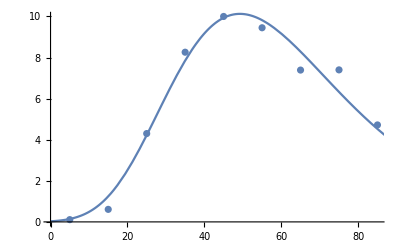

```mathematica
Show[ListPlot[{lc}],Plot[{lcm[t]},{t,0,95}]]
```

```mathematica
msnegsel=Table[{ms[[i,1]],ms[[i,2]]*Exp[0.045*ms[[i,1]]]},{i,Length[ms]}];
```

```mathematica
msnegselerr=Table[{ms[[i,1]],mserr[[i,2]]*Exp[0.045*ms[[i,1]]]},{i,Length[ms]}];
```

```mathematica
lcnegselm=NonlinearModelFit[lcnegsel,A Exp[-k Exp[-d t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[320.462 ⅇ^(-7.59953 ⅇ^(«1»))]

```mathematica
lcnegselm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 320.462 | 74.9281 | 4.27693 | 0.00522317
k | 7.59953 | 2.56862 | 2.95861 | 0.0253285
d | 0.0361277 | 0.010404 | 3.47246 | 0.0132639

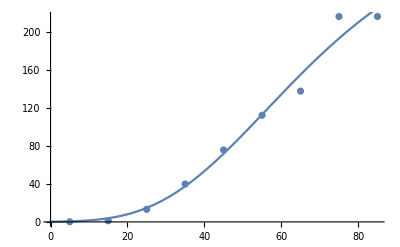

```mathematica
Show[ListPlot[{lcnegsel}],Plot[{lcnegselm[t]},{t,0,95}]]
```

```mathematica
lcdata=Drop[Drop[s,14,{4}],-3,{1,2,3}][[All,3]]
```

{0.,0.96,13.9,23.99,25.8,21.14,13.71,9.62,7.01,5.08}

```mathematica
ages=Range[5,95,10]
```

{5,15,25,35,45,55,65,75,85,95}

```mathematica
msfemale=Table[{ages[[i]],lcdata[[i]]},{i,1,Length[ages]}]
```

{{5,0.},{15,0.96},{25,13.9},{35,23.99},{45,25.8},{55,21.14},{65,13.71},{75,9.62},{85,7.01},{95,5.08}}

```mathematica
mspop=Drop[Drop[s,14,{4}],-3,{1,2,3}][[All,1]]*1000
```

{804100.,1.035×10^6,870300.,1.25×10^6,1.3874×10^6,1.2771×10^6,1.0355×10^6,810700.,499200.,117900.}

```mathematica
mscases=Drop[Drop[s,14,{}],-3,{1,2,3}][[All,3]]
```

{0.,10.,121.,300.,358.,270.,142.,78.,35.,6.}

```mathematica
msprop=mscases/mspop
```

{0.,9.66184×10^-6,0.000139033,0.00024,0.000258037,0.000211416,0.000137132,0.0000962131,0.0000701122,0.0000508906}

```mathematica
msfemaleerr=Table[{ages[[i]],Around[lcdata[[i]],100000*1.96*√(msprop[[i]](1-msprop[[i]])/mspop[[i]])]},{i,1,Length[ages]}]
```

{{5,0.},{15,1.00.6},{25,13.92.5},{35,24.02.7},{45,25.82.7},{55,21.12.5},{65,13.72.3},{75,9.62.1},{85,7.02.3},{95,5.4.}}

```mathematica
msfemalenegsel=Table[{msfemale[[i,1]],msfemale[[i,2]]*Exp[0.045*msfemale[[i,1]]]},{i,Length[msfemale]}];
```

```mathematica
msfemalenegselerr=Table[{msfemale[[i,1]],msfemaleerr[[i,2]]*Exp[0.045*msfemale[[i,1]]]},{i,Length[msfemale]-1}];
```

```mathematica
msfemalenegselm=NonlinearModelFit[msfemalenegsel,A Exp[-k Exp[-d t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[312.219 ⅇ^(-10.7071 ⅇ^(«1»))]

```mathematica
msfemalenegselm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 312.219 | 13.7694 | 22.6749 | 4.81731×10^-7
k | 10.7071 | 3.41465 | 3.13564 | 0.0201795
d | 0.0681729 | 0.00967064 | 7.04948 | 0.000407596

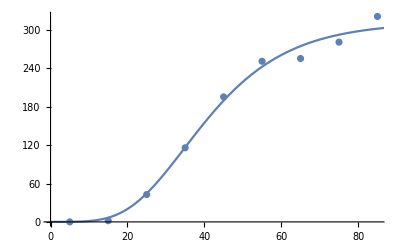

```mathematica
Show[ListPlot[{msfemalenegsel}],Plot[{msfemalenegselm[t]},{t,0,95}]]
```

```mathematica
msfemalenegselm=NonlinearModelFit[msfemalenegsel,A Exp[-k Exp[-d t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[312.219 ⅇ^(-10.7071 ⅇ^(«1»))]

```mathematica
msfemalenegselm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 312.219 | 13.7694 | 22.6749 | 4.81731×10^-7
k | 10.7071 | 3.41465 | 3.13564 | 0.0201795
d | 0.0681729 | 0.00967064 | 7.04948 | 0.000407596

```mathematica
msnegselm=NonlinearModelFit[msnegsel,A Exp[-k Exp[-d t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[320.462 ⅇ^(-7.59953 ⅇ^(«1»))]

```mathematica
msnegselm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 320.462 | 74.9281 | 4.27693 | 0.00522317
k | 7.59953 | 2.56862 | 2.95861 | 0.0253285
d | 0.0361277 | 0.010404 | 3.47246 | 0.0132639

```mathematica
lcnegselm=NonlinearModelFit[lcnegsel,A Exp[-k Exp[-d t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[31.5828 ⅇ^(-18.9807 «1»)]

```mathematica
lcnegselm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 31.5828 | 3.20482 | 9.85477 | 0.000594739
k | 18.9807 | 16.5479 | 1.14701 | 0.31532
d | 0.0780581 | 0.0255725 | 3.05242 | 0.0379384

```mathematica
msfemalem=NonlinearModelFit[msfemale,A Exp[-k Exp[-d t]-0.045t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[298.212 ⅇ^(-13.7953 «1»-«1»)]

```mathematica
msfemalem["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 298.212 | 13.1151 | 22.738 | 8.05998×10^-8
k | 13.7953 | 1.58877 | 8.68304 | 0.0000538278
d | 0.077302 | 0.00478152 | 16.1668 | 8.42714×10^-7

```mathematica
msm=NonlinearModelFit[ms,A Exp[-k Exp[-d t]-0.045t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[254.386 ⅇ^(-9.07525 «1»-«1»)]

```mathematica
msm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 254.386 | 37.0516 | 6.86571 | 0.000470321
k | 9.07525 | 1.09831 | 8.26294 | 0.00016997
d | 0.0446307 | 0.00541981 | 8.23472 | 0.000173241

```mathematica
lcm=NonlinearModelFit[lc,A Exp[-k Exp[-d t]-0.045t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[55.7896 ⅇ^(-5.91752 «1»-«1»)]

```mathematica
lcm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 55.7896 | 22.5364 | 2.47553 | 0.0685389
k | 5.91752 | 0.529686 | 11.1717 | 0.000365442
d | 0.0335996 | 0.00805445 | 4.17155 | 0.0140136

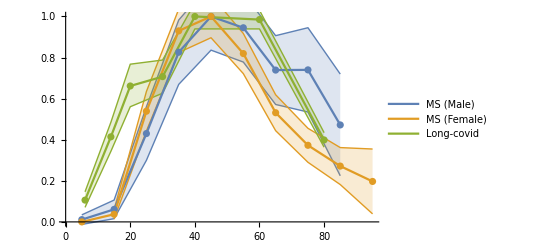

```mathematica
Show[ListPlot[{mserr.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemaleerr.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lcerr.{{1,0},{0,1/Max[lc[[All,2]]]}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick,IntervalMarkers->"Bands"],ListPlot[{ms.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemale.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lc.{{1,0},{0,1/Max[lc[[All,2]]]}}}]]
```

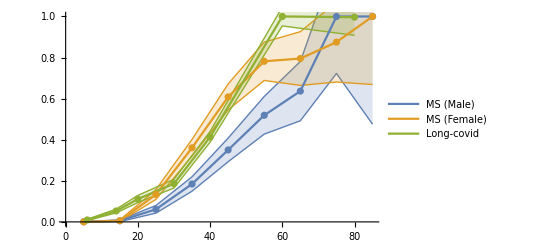

```mathematica
Show[ListPlot[{msnegselerr.{{1,0},{0,1/Max[msnegsel]}},msfemalenegselerr.{{1,0},{0,1/Max[msfemalenegsel]}},lcnegselerr.{{1,0},{0,1/Max[lcnegsel[[All,2]]]}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick,IntervalMarkers->"Bands"],ListPlot[{msnegsel.{{1,0},{0,1/Max[msnegsel]}},msfemalenegsel.{{1,0},{0,1/Max[msfemalenegsel]}},lcnegsel.{{1,0},{0,1/Max[lcnegsel[[All,2]]]}}}]]
```

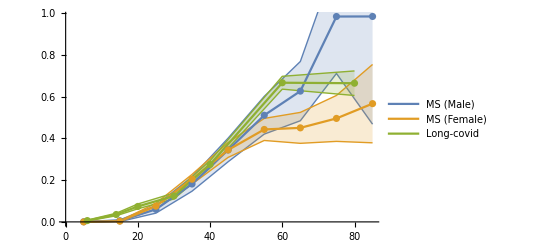

```mathematica
Show[ListPlot[{msnegselerr.{{1,0},{0,1/Max[ms[[All,2]]]/22}},msfemalenegselerr.{{1,0},{0,1/Max[msfemale[[All,2]]]/22}},lcnegselerr.{{1,0},{0,1/Max[lc[[All,2]]]/22}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick,IntervalMarkers->"Bands"],ListPlot[{msnegsel.{{1,0},{0,1/Max[ms[[All,2]]]/22}},msfemalenegsel.{{1,0},{0,1/Max[msfemale[[All,2]]]/22}},lcnegsel.{{1,0},{0,1/Max[lc[[All,2]]]/22}}}]]
```

```mathematica
(* With model fits
```

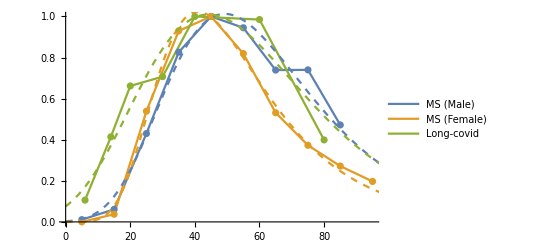

```mathematica
Show[ListPlot[{ms.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemale.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lc.{{1,0},{0,1/Max[lc[[All,2]]]}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick],ListPlot[{ms.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemale.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lc.{{1,0},{0,1/Max[lc[[All,2]]]}}}],Plot[{msm[t]/Max[ms[[All,2]]],msfemalem[t]/Max[msfemale[[All,2]]],lcm[t]/Max[lc[[All,2]]]},{t,0,100},PlotStyle->Dashed]]
```

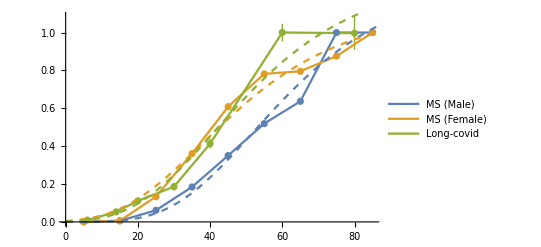

```mathematica
Show[ListPlot[{msnegsel.{{1,0},{0,1/Max[msnegsel]}},msfemalenegsel.{{1,0},{0,1/Max[msfemalenegsel]}},lcnegselerr.{{1,0},{0,1/Max[lcnegsel[[All,2]]]}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick],ListPlot[{msnegsel.{{1,0},{0,1/Max[msnegsel]}},msfemalenegsel.{{1,0},{0,1/Max[msfemalenegsel]}},lcnegsel.{{1,0},{0,1/Max[lcnegsel[[All,2]]]}}}],Plot[{msnegselm[t]/Max[msnegsel],msfemalenegselm[t]/Max[msfemalenegsel],lcnegselm[t]/Max[lcnegsel[[All,2]]]},{t,0,100},PlotStyle->Dashed]]
```

```mathematica
(* Setting d=0.045
```

```mathematica
msfemalem=NonlinearModelFit[msfemale,A Exp[-k Exp[-0.045 t]-0.045t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[453.968 ⅇ^(-7.2068 «1»-«1»)]

```mathematica
msm=NonlinearModelFit[ms,A Exp[-k Exp[-0.045t]-0.045t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[252.028 ⅇ^(-9.14147 «1»-«1»)]

```mathematica
lcm=NonlinearModelFit[lc,A Exp[-k Exp[-0.045 t]-0.045t],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[37.0224 ⅇ^(-6.50833 «1»-«1»)]

```mathematica
msfemalenegselm=NonlinearModelFit[msfemalenegsel,A Exp[-k Exp[-0.045 t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[359.155 ⅇ^(-5.46039 ⅇ^(«1»))]

```mathematica
msnegselm=NonlinearModelFit[msnegsel,A Exp[-k Exp[-0.045t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[275.842 ⅇ^(-10.2449 «1»)]

```mathematica
lcnegselm=NonlinearModelFit[lcnegsel,A Exp[-k Exp[-0.045 t]],{{A,10000},{k,40},{d,0.05}},t]
```

FittedModel[37.6046 ⅇ^(-6.37841 «1»)]

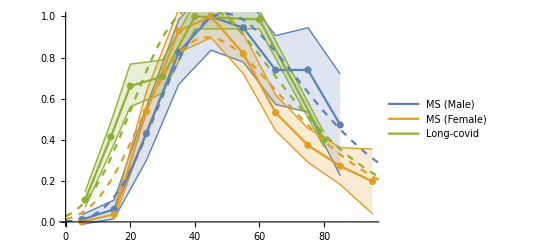

```mathematica
Show[ListPlot[{mserr.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemaleerr.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lcerr.{{1,0},{0,1/Max[lc[[All,2]]]}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick,IntervalMarkers->"Bands"],ListPlot[{ms.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemale.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lc.{{1,0},{0,1/Max[lc[[All,2]]]}}}],Plot[{msm[t]/Max[ms[[All,2]]],msfemalem[t]/Max[msfemale[[All,2]]],lcm[t]/Max[lc[[All,2]]]},{t,0,100},PlotStyle->Dashed]]
```

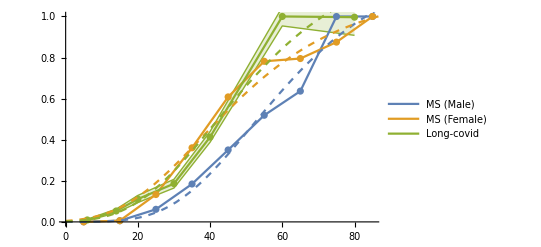

```mathematica
Show[ListPlot[{msnegsel.{{1,0},{0,1/Max[msnegsel]}},msfemalenegsel.{{1,0},{0,1/Max[msfemalenegsel]}},lcnegselerr.{{1,0},{0,1/Max[lcnegsel[[All,2]]]}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick,IntervalMarkers->"Bands"],ListPlot[{msnegsel.{{1,0},{0,1/Max[msnegsel]}},msfemalenegsel.{{1,0},{0,1/Max[msfemalenegsel]}},lcnegsel.{{1,0},{0,1/Max[lcnegsel[[All,2]]]}}}],Plot[{msnegselm[t]/Max[msnegsel],msfemalenegselm[t]/Max[msfemalenegsel],lcnegselm[t]/Max[lcnegsel[[All,2]]]},{t,0,100},PlotStyle->Dashed]]
```

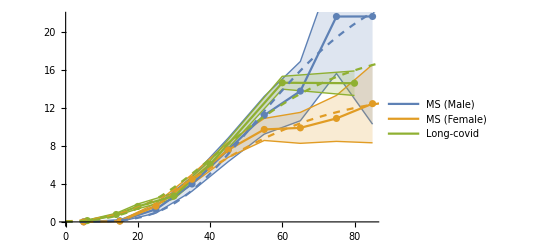

```mathematica
Show[ListPlot[{msnegselerr.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemalenegselerr.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lcnegselerr.{{1,0},{0,1/Max[lc[[All,2]]]}}},Joined->True,PlotLegends->{"MS (Male)","MS (Female)","Long-covid"},AxesStyle->Thick,IntervalMarkers->"Bands"],ListPlot[{msnegsel.{{1,0},{0,1/Max[ms[[All,2]]]}},msfemalenegsel.{{1,0},{0,1/Max[msfemale[[All,2]]]}},lcnegsel.{{1,0},{0,1/Max[lc[[All,2]]]}}}],Plot[{msnegselm[t]/Max[ms[[All,2]]],msfemalenegselm[t]/Max[msfemale[[All,2]]],lcnegselm[t]/Max[lc[[All,2]]]},{t,0,100},PlotStyle->Dashed]]
```